# 8. Relaciones binarias y conjuntos ordenados

## Ejemplos con Mathematica 6

## 1. Relaciones binarias

```mathematica
A={a,b,c};
R={{a,a},{b,b},{a,b},{b,c}};
```

### Ejemplo 8.1.

Sean A = {a, b, c, d, e, f, g, h} y R = {(a, a), (b, b), (c, c), (d, d), (e, e), (f, f), (g, g), (h, h), (a, b), (b, a)}. Determinar si R es reflexiva, simétrica, transitiva o antisimétrica, y comprobar si R es relación de orden o de equivalencia.

```mathematica
A={a,b,c,d,e,f,g,h};
R={{a,a},{b,b},{c,c},{d,d},{e,e},{f,f},{g,g},{h,h},{a,b},{b,a}};
Reflexiva=True;For[n=1,n≤Length[A],n++,If[Intersection[{{A[[n]],A[[n]]}},R]=={{A[[n]],A[[n]]}},Null,Reflexiva=False]];Simetrica=True;For[m=1,m≤Length[R],m++,If[Intersection[{{R[[m,2]],R[[m,1]]}},R]=={{R[[m,2]],R[[m,1]]}},Null,Simetrica=False]];
Transitiva=True;For[p=1,p≤Length[R],p++,For[q=1,q≤Length[R],q++,If[R[[p,1]]==R[[q,2]],If[Intersection[{{R[[q,1]],R[[p,2]]}},R]=={{R[[q,1]],R[[p,2]]}},Null,Transitiva=False]];];];Antisimetrica=True;For[r=1,r≤Length[R],r++,If[Intersection[{{R[[r,2]],R[[r,1]]}},R]=={{R[[r,2]],R[[r,1]]}}&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),Antisimetrica=False]];If[Reflexiva,Print["R es reflexiva"],Print["R no es reflexiva"]]If[Simetrica,Print["R es simétrica"],Print["R no es simétrica"]]If[Transitiva,Print["R es transitiva"],Print["R no es transitiva"]]If[Antisimetrica,Print["R es antisimétrica"],Print["R no es antisimétrica"]];If[Reflexiva&&Simetrica&&Transitiva,Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];If[Reflexiva&&Antisimetrica&&Transitiva,Print["R es una relación de orden"],Print["R no es relación de orden"]]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica

R es una relación de equivalencia

R no es relación de orden

## 2. Máximos y mínimos

### Ejemplo 8.2.

Sea A = {a, b, c, d, e, f, g, h, i} un conjunto ordenado con la relación binaria: R = {(a, a), (a, b), (a, c), (a, d), (a, e), (a, f), (a, h), (a, i), (b, b), (b, e), (b, f), (b, h), (b, i), (c, c), (d, d), (d, e), (d, f), (d, h), (d, i), (e, e), (e, f), (e, h), (e, i), (f, f), (f, i), (g, g), (g, i), (h, h), (h, i), (i, i)}. Calcular, si existen, el máximo y el mínimo de A.

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
maximo={};Do[maxi=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]=={},maxi=False],{m,1,Length[A]}];If[maxi,AppendTo[maximo,A[[n]]]];,{n,1,Length[A]}];If[maximo=={},Print["No tiene máximo"],Print["Máximo: ",maximo[[1]]]]
```

No tiene máximo

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
minimo={};Do[mini=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]=={},mini=False],{m,1,Length[A]}];If[mini,AppendTo[minimo,A[[n]]]];,{n,1,Length[A]}];If[minimo=={},Print["No tiene mínimo"],Print["Mínimo: ",minimo[[1]]]]
```

No tiene mínimo

## 3. Elementos maximales y minimales

### Ejemplo 8.3.

Sea A el mismo conjunto ordenado del ejemplo 8.2., calcular sus elementos maximales y minimales.

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
maximales={};Do[maximal=True;Do[If[Intersection[{{A[[n]],A[[m]]}},R]≠{}&&n≠m,maximal=False],{m,1,Length[A]}];If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];Print["Maximales: ",maximales]
```

Maximales: {c,i}

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
minimales={};Do[minimal=True;Do[If[Intersection[{{A[[m]],A[[n]]}},R]≠{}&&n≠m,minimal=False],{m,1,Length[A]}];If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];Print["Minimales: ",minimales]
```

Minimales: {a,g}

## 4. Cotas superiores e inferiores. Supremo e ínfimo

### Ejemplo 8.4.

Consideremos el mismo conjunto A ordenado del ejemplo 8.2. y sea B el subconjunto de A dado por B = {a, e, f, g, h}. Calculamos todas las cotas superiores e inferiores y el supremo e ínfimo, si existen.

```mathematica
A={a,b,c,d,e,f,g,h,i};
B={a,e,f,g,h};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
cotassuperiores={};Do[csuper=True;Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False],{m,1,Length[B]}];If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];If[cotassuperiores=={},Print["No hay cotas superiores"],Print["Cotas superiores: ",cotassuperiores];supremo={};Do[mini=True;Do[If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False],{m,1,Length[cotassuperiores]}];If[mini,AppendTo[supremo,cotassuperiores[[n]]]];,{n,1,Length[cotassuperiores]}];If[supremo=={},Print["No tiene supremo"],Print["Supremo: ",supremo[[1]]]]];
```

Cotas superiores: {i}

Supremo: i

```mathematica
A={a,b,c,d,e,f,g,h,i};
B={a,e,f,g,h};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
cotasinferiores={};Do[cinfer=True;Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False],{m,1,Length[B]}];If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];If[cotasinferiores=={},Print["No hay cotas inferiores"],Print["Cotas inferiores: ",cotasinferiores];infimo={};Do[maxi=True;Do[If[Intersection[{{cotasinferiores[[m]],cotasinferiores[[n]]}},R]=={},maxi=False],{m,1,Length[cotasinferiores]}];If[maxi,AppendTo[infimo,cotasinferiores[[n]]]];,{n,1,Length[cotasinferiores]}];If[infimo=={},Print["No tiene ínfimo"],Print["Ínfimo: ",infimo[[1]]]]];
```

No hay cotas inferiores

## 5. Diagramas de orden

### Ejemplo 8.5.

Consideremos el mismo conjunto A ordenado del ejemplo 8.2. Determinar su diagrama de orden.

Diagrama de orden:

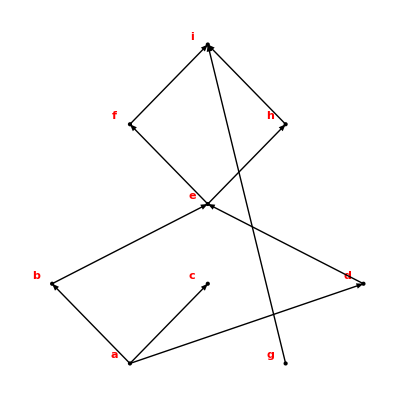

```mathematica
A={a,b,c,d,e,f,g,h,i};
R={{a,a},{a,b},{a,c},{a,d},{a,e},{a,f},{a,h},{a,i},{b,b},{b,e},{b,f},{b,h},{b,i},{c,c},{d,d},{d,e},{d,f},{d,h},{d,i},{e,e},{e,f},{e,h},{e,i},{f,f},{f,i},{g,g},{g,i},{h,h},{h,i},{i,i}};
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];B=A;t1=1;nivel=0;While[B≠{},minimales={};nivel++;Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False],{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,
{n1,1,Length[B]}];
B=Complement[B,minimales];
]
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];R1={};
Do[
Do[
If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,
R1=Union[R1,{R[[k1]]}];
];
,{j1,1,Length[A]}],{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];Do[t1++;puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2),{k1,1,cont}],
{j1,1,tabla[[Length[A],1]]}];Coord[elem_]:=Do[If[elem==tabla[[h1,2]],
Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];Do[Coord[A[[i1]]],{i1,1,Length[A]}];Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];
,{t1,1,Length[R]}];
Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```